#### Function for correcting the alpha angle due to not perfectly putting PS at the outer edges

```mathematica
alphafunc=Function[{y},180/π*ArcCos[(25^2+y^2+2*25^2-(25-y)^2)/(2*√2*25*√(25^2+y^2))]];
alphacorr=alphafunc[16.8];
```

#### Data input [corr_PSL2_(alt_base) --> large intw (-20 +10), correction selection with small PS, alternative baseline]

```mathematica
LSPosition={"C1","C2","R0","R1","R2","L0","L1","L2"};
Phi={-131.7,62.57,-52.31,-106.1,26.32,146.9,-166.8,98.35};
PhiError={1.2,1.51,0.98,2.3,2.68,0.7,1.9,1.91};
Sigma={46.17,49.72,61.63,52.89,95.65,58.13,59.25,54.22};
SigmaError={1.26,1.82,1.61,3.11,1.53,1.03,2.83,2.75};
Radius=1;
Alpha={-135,45,-45,-90-alphacorr,0+alphacorr,135,-180+alphacorr,90-alphacorr}

PhiList=Table[{Phi[[i]]*Pi/180,Radius},{i,Length[Phi]}] ;(*converting to radian and giving a fixed radius*)
LSPositionL=Thread[{LSPosition,Large}];
```

{-135,45,-45,-101.099,11.0989,135,-168.901,78.9011}

#### Data input [corr_PSL2_(alt_base)_4deg --> large intw (-20 +10), correction selection with small PS, alternative baseline, 4° rotation considered]

```mathematica
LSPosition={"C1","C2","R0","R1","R2","L0","L1","L2"};
Phi={-135.7,58.67,-56.27,-110.1,22.25,142.9,-170.9,94.36};
PhiError={1.21,1.52,0.98,2.3,2.68,0.7,1.9,1.86};
Sigma={46.22,49.79,61.71,53.16,95.6,58.15,59.42,54.19};
SigmaError={1.27,1.83,1.62,3.14,1.5,1.04,2.84,2.75};
Radius=1;
Alpha={-135,45,-45,-90-alphacorr,0+alphacorr,135,-180+alphacorr,90-alphacorr}

PhiList=Table[{Phi[[i]]*Pi/180,Radius},{i,Length[Phi]}] ;(*converting to radian and giving a fixed radius*)
LSPositionL=Thread[{LSPosition,Large}];
```

{-135,45,-45,-101.099,11.0989,135,-168.901,78.9011}

### Plotting of the polar plot

```mathematica
PhiPolarPlot=ListPolarPlot[List /@ PhiList, PlotMarkers->List/@LSPositionL,PolarAxes->Automatic,PolarAxesOrigin->{0,Radius+0.2}, PolarTicks->{"Degrees",Automatic},TicksStyle->Medium,PlotRange->1.5,PolarGridLines->Automatic,PlotLabel->Style[TraditionalForm[HoldForm["Corrected " OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large]
```

-Graphics-

### Plotting of the α-ϕ-Plot

{{-135,-136.46.},{45,59.50.},{-45,-56.62.},{-101.099,-110.53.},{11.0989,22.96.},{135,143.58.},{-168.901,-171.59.},{78.9011,94.54.}}

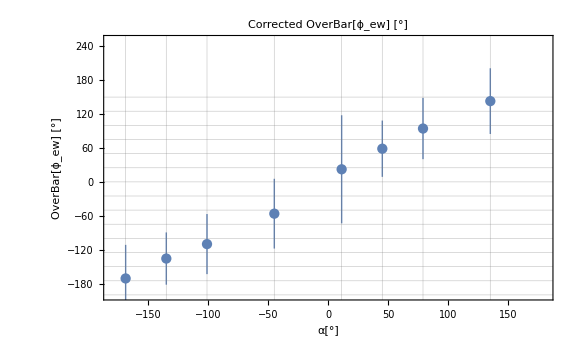

```mathematica
GridList=Table[i*25,{i,-200/25,150/25}];(*only for the graphic*)
AlphaPhiList=Table[{Alpha[[i]],Around[Phi[[i]],Sigma[[i]]]},{i,Length[Phi]}]
AlphaPhiPlot=ListPlot[AlphaPhiList,PlotRange->{{-180,180},{-200,250}},GridLines->{Alpha,GridList}, Axes->False,Frame->True, FrameTicksStyle->Medium, FrameLabel->{Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large], ImageSize->Large]
```

### Plotting the α-σ-Plot

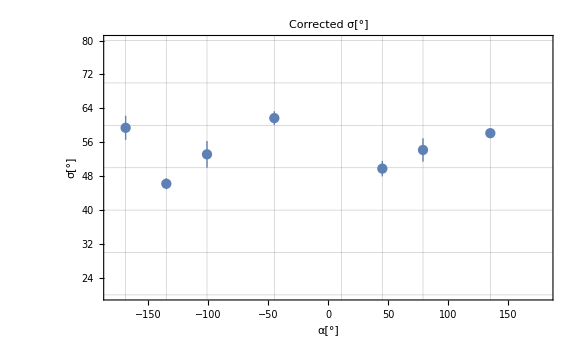

```mathematica
GridList=Table[i*10,{i,-200/25,150/10}];(*only for the graphic*)
AlphaSigmaList=Table[{Alpha[[i]],Around[Sigma[[i]],SigmaError[[i]]]},{i,Length[Sigma]}];
AlphaSigmaPlot=ListPlot[AlphaSigmaList,PlotRange->{{-180,180},{20,80}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameLabel->{"α[°]","σ[°]"},PlotLabel->Style["Corrected σ[°]",Large], ImageSize->Large]
```

## Klarifizierung des Konfidenzintervalls

{{-135,-135.7},{45,58.67},{-45,-56.27},{-101.099,-110.1},{11.0989,22.25},{135,142.9},{-168.901,-170.9},{78.9011,94.36}}

FittedModel[1.44421+1.05454 α]

1.44421+1.05454 α-2.44691 √(1.20455-0.000727982 α+0.0000162052 α^2)

1.44421+1.05454 α+2.44691 √(1.20455-0.000727982 α+0.0000162052 α^2)

-3.91944

1.17625

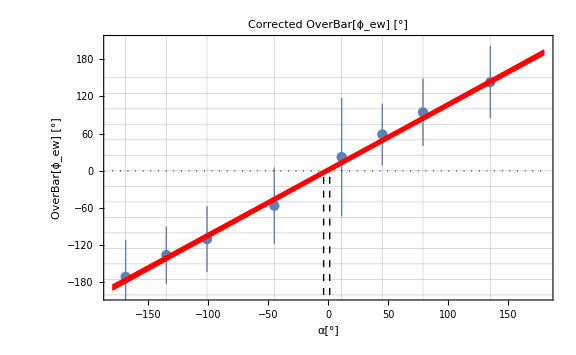

```mathematica
GridList=Table[i*25,{i,-200/25,150/25}];(*only for the graphic*)AlphaPhiPlot=ListPlot[AlphaPhiList,PlotRange->{{-180,180},{-200,210}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameLabel->{"α[°]",TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large];
AlphaPhiFitList=Table[{Alpha[[i]],Phi[[i]]},{i,Length[Phi]}]
fit=LinearModelFit[AlphaPhiFitList,α,α,Weights->1/PhiError^2,VarianceEstimatorFunction->(1&)]
LowerPredictionBand=fit["SinglePredictionBands"][[1]]
UpperPredictionBand=fit["SinglePredictionBands"][[2]]

AssumedPhi=0;
MinimumAlpha=Solve[UpperPredictionBand==AssumedPhi,α][[1,1,2]]
MaximumAlpha=Solve[LowerPredictionBand==AssumedPhi,α][[1,1,2]]

ErrorGraphic=Show[AlphaPhiPlot,
Plot[{fit["BestFit"],fit["SinglePredictionBands"]},{α,-180,180},PlotStyle->Red,Filling->{2->{1},3->{1}}],
Graphics[{Dashed,Line[{{MinimumAlpha,-200},{MinimumAlpha,AssumedPhi}}]}],
Graphics[{Dashed,Line[{{MaximumAlpha,-200},{MaximumAlpha,AssumedPhi}}]}],
Graphics[{Dotted,Line[{{-180,0},{180,0}}]}]]
(*Export["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/ConfidencePlot.pdf",ErrorGraphic,"PDF"]*)
```

## Klarifizierung des Konfidenzintervalls 2

FittedModel[1.44421+1.05454 α]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.44421 | 0.452277 | 3.19319 | 0.0187606
α | 1.05454 | 0.00402556 | 261.96 | 2.08829×10^-13

| DF | SS | MS | F-Statistic | P-Value
α | 1 | 68623.2 | 68623.2 | 1839.57 | 1.07509×10^-8
Error | 6 | 223.824 | 37.304 |  | 
Total | 7 | 68847. |  |  |

0.996207

59.78

15.3452

-61.596+1.05454 α

64.4844+1.05454 α

-61.1495

58.4105

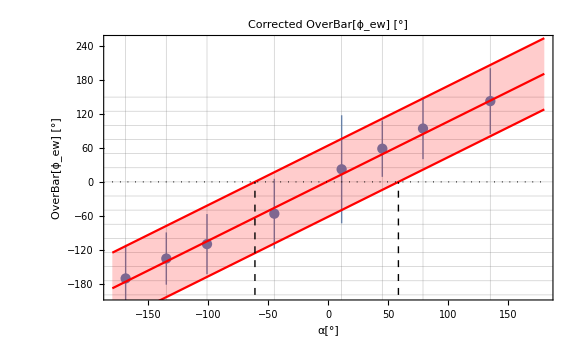

```mathematica
AlphaPhiPlot=ListPlot[AlphaPhiList,PlotRange->{{-180,180},{-200,250}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameTicksStyle->Medium,FrameLabel-> {Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large];
AlphaPhiFitList=Table[{Alpha[[i]],Phi[[i]]},{i,Length[Phi]}];
fit=LinearModelFit[AlphaPhiFitList,α,α,Weights->1/PhiError^2,VarianceEstimatorFunction->(1&)]
fit["ParameterTable"]
fit["ANOVATable"]
fit["AdjustedRSquared"]
MeanSigma=Mean[Sigma]
StandardDeviation[Sigma]
LowerPredictionBand=fit["BestFit"];
UpperPredictionBand=fit["BestFit"];
LowerPredictionBand=LowerPredictionBand-fit["BestFitParameters"][[2]]*MeanSigma
UpperPredictionBand=UpperPredictionBand+fit["BestFitParameters"][[2]]*MeanSigma

AssumedPhi=0;
MinimumAlpha=Solve[UpperPredictionBand==AssumedPhi,α][[1,1,2]]
MaximumAlpha=Solve[LowerPredictionBand==AssumedPhi,α][[1,1,2]]

ErrorGraphic=Show[ListPlot[AlphaPhiList,PlotRange->{{-180,180},{-200,250}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameTicksStyle->Medium,FrameLabel-> {Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large],
Plot[{fit["BestFit"],LowerPredictionBand,UpperPredictionBand},{α,-180,180},PlotStyle->Red,Filling->{2->{1},3->{1}}],
Graphics[{Dashed,Line[{{MinimumAlpha,-200},{MinimumAlpha,AssumedPhi}}]}],
Graphics[{Dashed,Line[{{MaximumAlpha,-200},{MaximumAlpha,AssumedPhi}}]}],
Graphics[{Dotted,Line[{{-180,0},{180,0}}]}],
PlotLabels->"Expressions"]
```